```mathematica
$PlotTheme="Scientific";
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xfrac}","\\usepackage[T1]{fontenc}"}];
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
ctdfracterms=20;
```

```mathematica
Z[s_]:=Which[Im[s]≥1,ContinuedFractionK[If[n==1,s,-1/2 (-1+n) (-3+2 n)],-s^2-3/2+2 n,{n,1,ctdfracterms}],-1<Im[s]<1,ⅈ*√π*Exp[-s^2]*(1+Erf[ⅈ*s]),Im[s]≤-1,2*ⅈ*√π*Exp[-s^2]+Conjugate[ContinuedFractionK[If[n==1,Conjugate[s],-1/2 (-1+n) (-3+2 n)],-Conjugate[s]^2-3/2+2 n,{n,1,ctdfracterms}]],True,"Error"]
```

```mathematica
P[k_,ω_]:=1+ω/(√2*k)*Z[ω/(√2*k)]
```

```mathematica
soln[k_]:=FindRoot[P[k,ω]==k^2,{ω,ⅈ}][[1,2]]
```

```mathematica
imonly[tab_]:=Table[{tab[[n,1]],Im[tab[[n,2]]]},{n,1,Length[tab]}]
```

```mathematica
reim[tab_]:={Table[{tab[[n,1]],Re[tab[[n,2]]]},{n,1,Length[tab]}],Table[{tab[[n,1]],Im[tab[[n,2]]]},{n,1,Length[tab]}]}
```

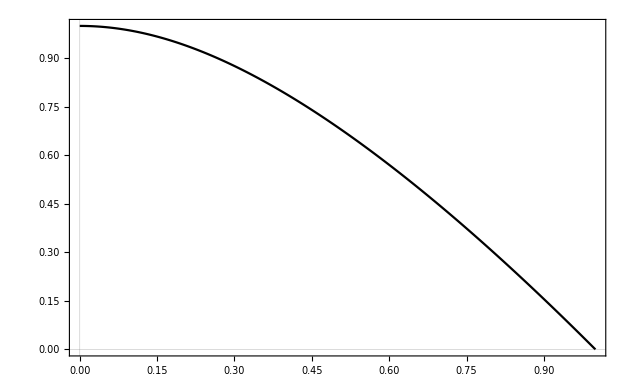

```mathematica
dispersionfig=Plot[Im[soln[k]],{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->Black,PlotPoints->1000]
```

```mathematica
Export["fig_dispersionrelation.pdf",dispersionfig];
```

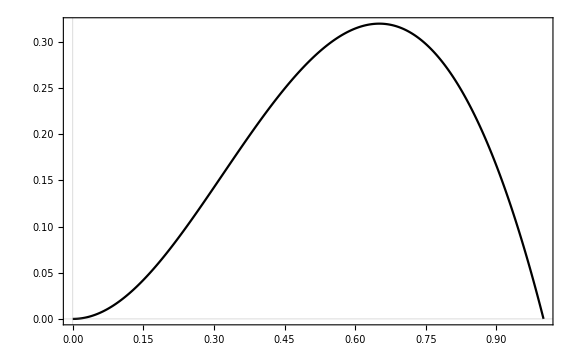

```mathematica
Plot[1-k^2-Im[soln[k]]^2,{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.5],MaTeX["\\sfrac{\\left[\\sigma^2\\left(k_\\text{J}^2-k^2\\right)-\\eta(k)^2\\right]}{k_\\text{J}^2\\sigma^2}",Magnification->1.5]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->Black,PlotPoints->1000,ImageSize->Large]
```

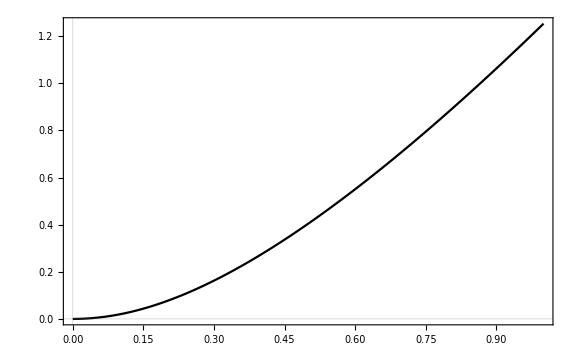

```mathematica
zerofig=Plot[(1-k^2-Im[soln[k]]^2)/Im[soln[k]],{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.5],MaTeX["\\frac{\\sigma^2\\left(k_\\text{J}^2-k^2\\right)-\\eta(k)^2}{k_\\text{J}\\eta(k)\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->Black,PlotPoints->1000,ImageSize->Large(*,ImagePadding->{{300,0},{0,0}}*)]
```

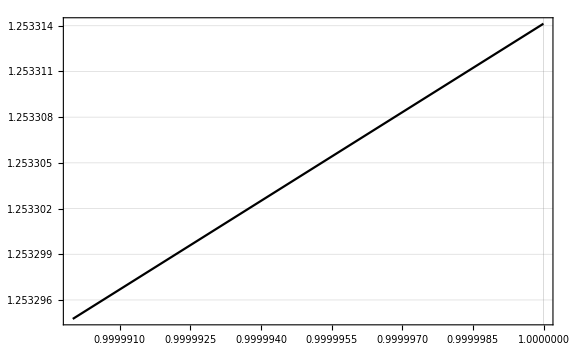

```mathematica
zerofigzoomm=Plot[(1-k^2-Im[soln[k]]^2)/Im[soln[k]],{k,0.99999,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.5],MaTeX["\\frac{\\sigma^2\\left(k_\\text{J}^2-k^2\\right)-\\eta(k)^2}{k_\\text{J}\\eta(k)\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->Black,PlotPoints->1000,ImageSize->Large(*,ImagePadding->{{300,0},{0,0}}*),GridLines->{{1},Automatic}]
```

```mathematica
N[√(π/2)]
```

1.25331

```mathematica
Export["fig_simplezero.pdf",zerofig];
```

```mathematica
ps8log={{colors[[1]],Dotted},{colors[[2]],Dashing[{0.005,0.005}]},{colors[[3]],Dashing[{0.01,0.01}]},{colors[[4]],Dashing[{0.02,0.02}]}};
```

```mathematica
ps8=Join[{Black},ps8log];
```

```mathematica
pllog={MaTeX["k_\\text{J}\\sigma-\\frac{3\\sigma k^2}{2 k_\\text{J}}"],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{15\\sigma k^4}{8 k_\\text{J}^3}"],MaTeX["k_\\text{J}\\sigma-\\cdots-\\frac{147\\sigma k^6}{16 k_\\text{J}^5}"],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{9531\\sigma k^8}{128 k_\\text{J}^7}"]};
```

```mathematica
pl=Join[{None},pllog];
```

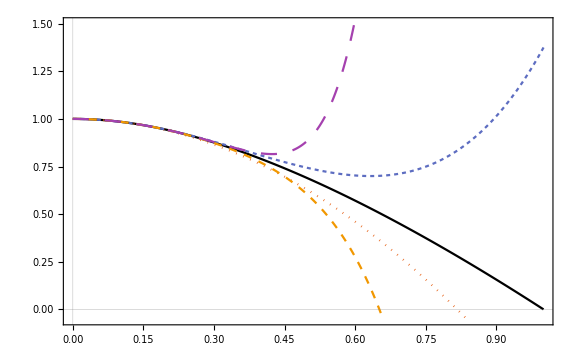

```mathematica
asymptoticfig=Plot[{Im[soln[k]],1-3/2*k^2,1-3/2*k^2+15/8*k^4,1-3/2*k^2+15/8*k^4-147/16*k^6,1-3/2*k^2+15/8*k^4-147/16*k^6+9531/128*k^8},{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8,PlotPoints->1000,ImageSize->Large,PlotLegends->pl,PlotRange->{Full,{-0.05,1.5}}]
```

```mathematica
Export["figasymptotic.pdf",asymptoticfig,ImageResolution->1000];
```

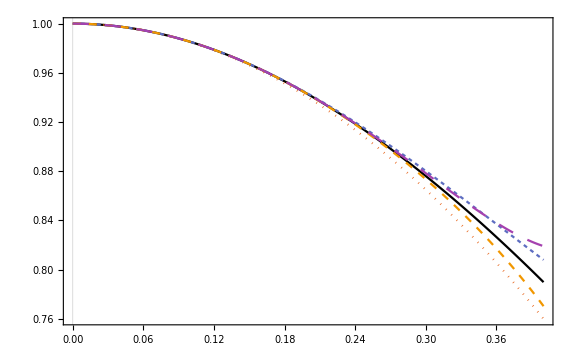

```mathematica
Plot[{Im[soln[k]],1-3/2*k^2,1-3/2*k^2+15/8*k^4,1-3/2*k^2+15/8*k^4-147/16*k^6,1-3/2*k^2+15/8*k^4-147/16*k^6+9531/128*k^8},{k,0,0.4},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8,PlotPoints->1000,ImageSize->Large,PlotLegends->pl]
```

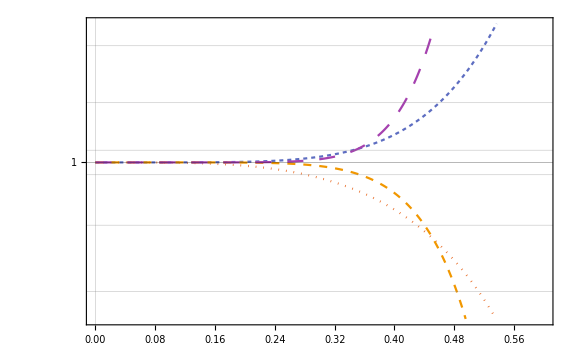

```mathematica
LogPlot[{(1-3/2*k^2)/Im[soln[k]],(1-3/2*k^2+15/8*k^4)/Im[soln[k]],(1-3/2*k^2+15/8*k^4-147/16*k^6)/Im[soln[k]],(1-3/2*k^2+15/8*k^4-147/16*k^6+9531/128*k^8)/Im[soln[k]]},{k,0,0.6},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],MaTeX["\\sfrac{\\text{Series}}{\\text{Exact}}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8log,PlotPoints->1000,ImageSize->Large,GridLines->{{0},{0.9,0.95,0.99,{1,Directive[Medium,Black]},1.01,1.05,1.1}},PlotLegends->pllog,PlotRange->{Automatic,{0.88,1.12}}]
```

```mathematica
(1-3/2*0.3^2)/Im[soln[0.3]]
```

0.987336

```mathematica
laxsticks={Automatic,{MaTeX["1-2\\times 10^{-4}"]}};
```

```mathematica
laxsticks={{{{1-1*10^-2,MaTeX["-10^{-2}+1"]},{1-1*10^-3,MaTeX["-10^{-3}+1"]},(*{1-5*10^-4,MaTeX["-5\\!\\times \\!10^{-4}+1"]},{1-1*10^-4,MaTeX["-10^{-4}+1"]},*){1,1},(*{1+1*10^-4,MaTeX["10^{-4}+1"]},*){1+1*10^-3,MaTeX["10^{-3}+1"]},{1+1*10^-2,MaTeX["10^{-2}+1"]}},None},{Automatic,None}};
```

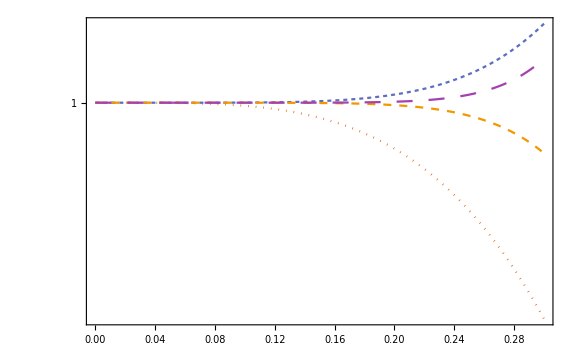

```mathematica
asymptoticlogfig=LogPlot[{(1-3/2*k^2)/Im[soln[k]],(1-3/2*k^2+15/8*k^4)/Im[soln[k]],(1-3/2*k^2+15/8*k^4-147/16*k^6)/Im[soln[k]],(1-3/2*k^2+15/8*k^4-147/16*k^6+9531/128*k^8)/Im[soln[k]]},{k,0,0.3},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],MaTeX["\\sfrac{\\text{Series}}{\\text{Exact}}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8log,PlotPoints->1000,ImageSize->Large,GridLines->{{0},{1-1*10^-2,1-1*10^-3,1,1+1*10^-3}},PlotLegends->pllog,PlotRange->(*{Automatic,{1-2*10^-4-2*10^-5,1+10^-4+4*10^-5}}*)Full,FrameTicks->laxsticks]
```

```mathematica
Export["figasymptoticlog.pdf",asymptoticlogfig,ImageResolution->1000];
```